# AntonAntonov/MosaicPlot

Mosaic plots for datasets and lists of records

## Paclet Manifest

"Documentation"

"English"

"Guides"

"ReferencePages"

"Symbols"

"MakeTooltipTable.nb"DocumentationEnglishReferencePagesSymbolsMakeTooltipTable.nb

"MosaicPlot.nb"DocumentationEnglishReferencePagesSymbolsMosaicPlot.nb

"Tutorials"

"Mosaicplotsfordatavisualization.nb"DocumentationEnglishTutorialsMosaicplotsfordatavisualization.nb

"Mosaicplotsfornumericalvariablesviacategoricalmapping.nb"DocumentationEnglishTutorialsMosaicplotsfornumericalvariablesviacategoricalmapping.nb

"Kernel"

"MosaicPlot.wl"KernelMosaicPlot.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

### Basic Description

The paclet provides the function MosaicPlot that summarizes the conditional probabilities of co-occurrence of categorical values in a Dataset object or a list of records of the same length.

### Details

If a list of records is given to MosaicPlot then the list is assumed to be a full array and the columns to represent categorical values.

Note, that if a column is numerical, but has a small number of different values then it can be seen as categorical.

This paclet is based in the paclet "AntonAntonov/TriesWithFrequencies".

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["AntonAntonov`MosaicPlot`"];
```

### Basic Examples

Get an example dataset (Titanic data):

```mathematica
dsTitanic=ResourceFunction["ExampleDataset"][{"MachineLearning","Titanic"}];
dsTitanic[1;;-1;;300]
```

-Graphics-

Make a mosaic plot for categorical columns:

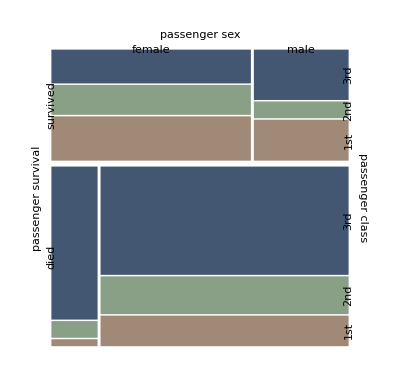

```mathematica
MosaicPlot[dsTitanic[All,{4,3,1}]]
```

### Scope

Rotate labels, specify column names, and column names offset and style:

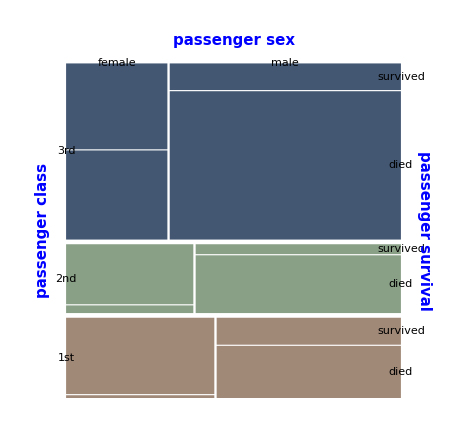

```mathematica
columnNames=Normal@Keys@dsTitanic[[1]];
MosaicPlot[Normal@dsTitanic[[All,{1,3,4}]][Values],"Gap"->0.014,"ColumnNamesOffset"->0.07,"ColumnNames"->Map[Style[#,Bold,Blue,FontSize->15]&,columnNames[[{1,3,4}]]],"LabelRotation"->{{3,1},{1,1}},ImageSize->Large]
```

Make a random dataset:

```mathematica
SeedRandom[35];
dsData=ResourceFunction["RandomTabularDataset"][{30,3},"Generators"->{CharacterRange["a","d"],CharacterRange["A","D"],CharacterRange["1","3"]}];
```

Make different mosaic plots using different color rules:

```mathematica
t=MosaicPlot[dsData,PlotLabel->If[TrueQ[#===None],"None",#],ColorRules->ReleaseHold[#],"Gap"->0.025,"GapFactor"->0.6,ImageSize->230]&/@{{},None,Automatic,{_->GrayLevel[0.7]},HoldForm[{1->Green,2->Blue,3->Red}],HoldForm[{-2->Blue,-1->Red}],HoldForm[{2->Blue}],HoldForm[{2->{Pink,Blue}}],HoldForm[{2->ColorData[11,"ColorList"]}]};
Grid[ArrayReshape[t,{3,3},""],Dividers->All]
```

-Graphics-

## Source & Additional Information

### Creator

Anton Antonov

### Source Control Repository

https://github.com/antononcube/WL-MosaicPlot-paclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Data analysis

Bayesian classifier

Mosaic

Mosaic plot

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

ExampleDataset

RandomTabularDataset

ImportCSVToDataset

### Original Source References and Attributions

Mosaic plots for data visualization | Mathematica for prediction algorithms

Enhancements of MosaicPlot | Mathematica for prediction algorithms

### Links

MathematicaForPrediction/MosaicPlot.m at master · antononcube/MathematicaForPrediction · GitHub

TriesWithFrequencies | Wolfram Language Paclet Repository

### Compatibility

#### Wolfram Language Version

11.3+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

WL system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

WL built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.